```mathematica
ClearAll["Global`*"]
Needs["ComputerArithmetic`"]
(*Needs["SciDraw`"]*)

mypath = "/home/leon/Dropbox/Mathematica/Space/Exp/";
CreateDirectory[mypath] ;

monitoredFindRoot[args__] := Module[{s = 0, e = 0, j = 0},
{FindRoot[args, StepMonitor :> s++, EvaluationMonitor :> e++, 
Jacobian -> {Automatic, EvaluationMonitor :> j++}], "Steps" -> s, 
"Evaluations" -> e, "Jacobian Evaluations" -> j}]
linearmesh[a_, b_, n_Integer /; n > 1] := Range[a, b, (b - a)/(n - 1)] ;
(* Parameters *)
```

CreateDirectory::filex: /home/leon/Dropbox/Mathematica/Space/Exp/ already exists.

```mathematica
PARAM = ( 
	Jee = 1.1 ; Jei = 1.5 ; Jie = 1.8 ; Jii = 1.8 ;
	Ie0 = .85 ; Ii0 = .85 ;
	λe = .125 ; λi = .075 ;
	L = 3 ;
) 
PARAM

Λ = { {λe,0}, {0,λi} } ;
J = { {Jee,-Jei}, {Jie,-Jii}} ;
Det[J]
```

0.72

```mathematica
r0 = {(Ie0 Jii-Jei Ii0)/(2 Jei Jie - 2 Jee Jii),(Ie0 Jie-Jee Ii0)/(2 Jei Jie-2 Jee Jii)} ;

Γmax[σ0_] = -((Ii0 Jei-Ie0 Jii) σ0^2)/(Jei (λe^2+σ0^2)) ; (* norm. to σ0 *)
Iext[x_,Γi0_,σ0_] = {Ie0, Ii0 + Γi0 /Sqrt[2 Pi] /σ0 Exp[-x x/(2 σ0^2 )]} ;
d2Iext[x_,Γi0_,σ0_] = {0,(ⅇ^(-x^2/(2 σ0^2)) x^2 Γi0)/(√(2 π) (σ0^2)^(5/2))-(ⅇ^(-x^2/(2 σ0^2)) Γi0)/(√(2 π) (σ0^2)^(3/2))} ;
rPos[x_,Γi0_,σ0_] = Simplify[ 1/2 ( Λ^2 . Inverse[J] . d2Iext[x,Γi0,σ0] - Inverse[J] . Iext[x,Γi0,σ0] ) ] ;

rNeg[x_,xc_,Γi0_,σ0_] = Simplify[ {0, λi^2/2/Jii ( Part[Iext[x,Γi0,σ0],2]/λi^2 - Part[d2Iext[x,Γi0,σ0],2] 
						+ 2 Jie/λe (1/λi^2-1/λe^2) Cosh[x/λe]  
								Integrate[Exp[-y/λe] Part[rPos[y,Γi0,σ0],1],{y,xc,Infinity}] ) }, σ0>0] ;
```

```mathematica
uE[xc_,Γi0_,σ0_] = Simplify[ ( Ie0 + 2 Jee/λe Cosh[xc/λe] Integrate[Exp[-y/λe] 
						Part[rPos[y,Γi0,σ0],1],{y,xc,Infinity}] 
					- 2 Jei/λi ( Cosh[xc/λi] Integrate[Exp[-y/λi] 
						Part[rPos[y,Γi0,σ0],2],{y,xc,Infinity}] 
						+ Exp[-xc/λi] Integrate[Cosh[y/λi] 
						 Part[rNeg[y,xc,Γi0,σ0],2],{y,0,xc}] ) ), σ0>0 ] ;

(*uI[xc_,Γi0_,σ0_] = Simplify[( Iext[xc,Γi0,σ0][[2]] + 2 Jie/λe Cosh[xc/λe] Integrate[Exp[-y/λe] 
							Part[rPos[y,Γi0,σ0],1],{y,xc,Infinity}] 
						- 2 Jii/λi ( Cosh[xc/λi] Integrate[Exp[-y/λi] 
							Part[rPos[y,Γi0,σ0],2],{y,xc,Infinity}] 
						+ Exp[-xc/λi] Integrate[Cosh[y/λi] 
							Part[rNeg[y,xc,Γi0,σ0],2],{y,0,xc}] ) ), σ0>0 ];
*)	
(*					
uE[x_,xc_,Γi0_,σ0_] = Simplify[( Ie0 + 2 Jee/λe Cosh[x/λe] Integrate[Exp[-y/λe] 
						Part[rPos[y,Γi0,σ0],1],{y,xc,Infinity}] 
					- 2 Jei/λi ( Cosh[x/λi] Integrate[Exp[-y/λi] 
							Part[rPos[y,Γi0,σ0],2],{y,xc,L/2}]
							+ Cosh[x/λi] Integrate[Exp[-y/λi] 
							Part[rNeg[y,xc,Γi0,σ0],2],{y,x,xc}] 
						+ Exp[-x/λi] Integrate[Cosh[y/λi] 
							Part[rNeg[y,xc,Γi0,σ0],2],{y,0,x}] ) ), σ0>0 ]; *)
							
xcE[σ0_,Γi0_] := xc /. First[monitoredFindRoot[ uE[xc,Γi0,σ0], {xc, σ0, 2 σ0}, Method -> "Secant"]] ;
```

```mathematica
rI[x_,σ0_,Γi0_] := rNeg[x,xcE[σ0,Γi0],Γi0,σ0][[2]]
minRi[σ0_,Γi0_] := First[FindMinimum[rI[x,σ0,Γi0],{x,σ0}]]
zeroRi[σ0_,Γi0_] := x/. First[monitoredFindRoot[rI[x,σ0,Γi0], {x, σ0, 2 σ0}, Method -> "Secant"] ] ;
```

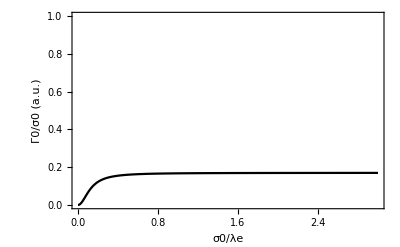

```mathematica
(* rE==0 line *)
Γmax[σ0_] = -((Ii0 Jei-Ie0 Jii) σ0^2)/(Jei (λe^2+σ0^2)) ; (* norm. to σ0 *)
xcEplt = Plot[Γmax[σ0], {σ0, 0, .375/λe}, PlotStyle->Black, PlotRange->All];
Show[xcEplt,PlotRange->{0,1}, AxesOrigin -> {0, 0},
		Frame -> {{True, False}, {True, False}},
	FrameLabel -> {"σ0/λe", "Γ0/σ0 (a.u.)"}]
```

```mathematica
xcIplt = ContourPlot[minRi[σ0,Γi0],{σ0,.075/λe,.2/λe},{Γi0,0,1},ColorFunction -> (If[# < 0, Lighter[White, Abs[#]],
Lighter[White, #]] &), ColorFunctionScaling -> False, FrameLabel -> {"σ0 (mm)", "Γ0 (a.u.)"}, Contours->{0}] ;
xcEplt = Plot[Γmax[σ0], {σ0, 0.075, .375}, PlotStyle->Black, PlotRange->All, AxesOrigin -> {0, 0}] ;
xcEzoom = Graphics[Inset[Plot[Γmax[σ0], {σ0, 0.075, .375}, PlotStyle->Black, PlotRange->{{.075,.375}, {0,Ceiling[100 Γmax[.375]]/100//N}},
Ticks->{{.075,.175,.275,.375}, linearmesh[0,Ceiling[100 Γmax[.375]]/100 //N,4]}, FrameLabel -> {"σ0 (mm)", "Γ0 (a.u.)"}],{.29,.8}] ] ;
Show[xcIplt,xcEplt,xcEzoom,PlotRange->{0,1}, AxesOrigin -> {0, 0},FrameTicks->{{.075,.175,.275,.375},{0,.2,.4,.6,.8,1}},Frame -> {{True, False}, {True, False}}]
```

```mathematica
xcVsΓ0 := (
	xcList = {} ;
	rEList = {} ;
	rIList = {} ;
	
	For[l=1,l<=Length[Γi0List],l++,
		Γi0 = Γi0List[[l]] ; 
		XC = xcE[σ0,Γi0] ;
		AppendTo[xcList,XC] ; 

		
		If[XC<x0,AppendTo[rEList, rPos[x0,Γi0,σ0][[1]] ], AppendTo[rEList, 0 ] ]  ; 
		If[XC<x0,AppendTo[rIList, rPos[x0,Γi0,σ0][[2]] ], AppendTo[rIList, rNeg[x0,XC,Γi0,σ0][[2]] ] ]  ;

	] ;

	xcList = xcList /. L/2 -> 0 ;
)
```

```mathematica
σ0 = .1 ; 
xMaxE = σ0 Sqrt[3 λe^2 + σ0^2]/λe
xMaxI = σ0 Sqrt[3 λi^2 + σ0^2]/λi
```

0.190788

0.218581

```mathematica
σ0 = .15 ; 
x0 = .125 ;
λe = .125 ; λi = .075 ;
Γi0List = linearmesh[0,1,20] //N ;
xcVsΓ0

data = Transpose@{Γi0List,xcList};
datarE = Transpose@{Γi0List,rEList/r0[[1]]};
rEPlt = ListLinePlot[datarE,FrameLabel->{"Γi0","Norm. Rates"},
					Frame->{{True,False},{True,False}},
					PlotRange->All, PlotMarkers->{●, 10},PlotStyle->Red]; 

datarI = Transpose@{Γi0List,rIList/r0[[2]]};
rIPlt = ListLinePlot[datarI,FrameLabel->{"Γi0","Norm. Rates"},
					Frame->{{True,False},{True,False}},
					PlotRange->All,PlotMarkers->{●, 10}, PlotStyle->Blue];
Show[rEPlt,rIPlt,PlotRange->All]

fileName = StringJoin[{mypath,"/xcVsG0_Cff_",ToString[NumberForm[σ0,{4,4}]],".dat"}] 
Export[fileName,data,"Table"] ;

fileName = StringJoin[{mypath,"/rEVsG0_x0_",ToString[NumberForm[x0,{4,4}]],"_Cff_",ToString[NumberForm[σ0,{4,4}]],".dat"}] 
Export[fileName,datarE,"Table"] ;

fileName = StringJoin[{mypath,"/rIVsG0_x0_",ToString[NumberForm[x0,{4,4}]],"_Cff_",ToString[NumberForm[σ0,{4,4}]],".dat"}] 
Export[fileName,datarI,"Table"] ;
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

1.22249

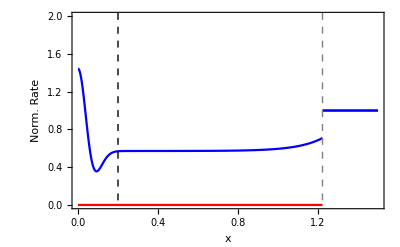

```mathematica
σ0 = .05 ; Γ0 = .05 ;
XC = xcE[σ0,Γ0]

posPlt = Plot[{rPos[x,Γ0,σ0][[1]]/r0[[1]], rPos[x,Γ0,σ0][[2]]/r0[[2]]}, {x, XC, L/2}, PlotRange -> All, AxesOrigin -> {0, -0.1},
   	Frame -> {{True, False}, {True, False}}, PlotStyle -> {Red,Blue}] ;

negPlt= Plot[{0,rNeg[x,XC,Γ0,σ0][[2]]/r0[[2]]}, {x, 0, XC}, PlotRange -> All, AxesOrigin -> {0, -0.1},
   	Frame -> {{True, False}, {True, False}}, FrameLabel -> {"x", "Rate"}, PlotStyle -> {Red,Blue}] ;
 
σ0line = Graphics[ {Black, Dashed, Line[{{4 σ0, 5}, {4 σ0, 0}} ] } ] ; 
xcline = Graphics[ {Gray, Dashed, Line[{{XC, 5}, {XC, 0}} ] } ] ;  

Fig = Show[posPlt,negPlt,xcline,σ0line, PlotRange->{0,2},FrameLabel -> {"x", "Norm. Rate"}]
```